```mathematica
(*displayData=Import["displayTbl.fits","Table"];*)
rawdata=Import["C:\\Users\\DELL\\Downloads\\GRB_Redshit_List_final_lat.txt", "Table"];
(** Only GRBs with TS > 20.0 and fitted with SPL are selected. **)
```

```mathematica
TableForm[sigdata,TableHeadings->{None,rawdata[[1,All]]}];
```

```mathematica
rawdata[[1]]
```

{GRB_NAME,GBM_ID,OPT,OPT_beta,XRT,GBM,LAT,z,AG_temp_decay_model,BPL_temp_ind1,BPL_temp_ind1_err,BPL_temp_ind2,BPL_temp_ind2_err,SPL_temp_ind1,SPL_temp_ind1_err,LAT_spec_ind,LAT_spec_err_ind}

```mathematica
sigdata=SortBy[Select[rawdata,(#[[10]]*#[[11]]!=0.0)&],#[[12]]&];
```

```mathematica
sigdata
```

{{100414A,100414097,Y,Y,Y,Y,Y,1.37,BPL,1.804,0.217,0.315,0.55,1.266,0.13,-1.801,0.118},{080916C,80916009,Y,Y,Y,Y,Y,4.35,BPL,1.609,0.213,0.359,0.288,1.128,0.118,-1.86,0.536},{110731A,110731465,Y,Y,Y,Y,Y,2.83,BPL,1.771,0.114,0.389,1.071,1.534,0.117,-2.288,0.155},{221009A,221009553,Y,Y,Y,Y,Y,0.151,BPL,1.58,0.46,0.85,0.23,1.15,0.13,-1.79,0.05},{171010A,171010792,Y,Y,Y,Y,Y,0.33,BPL,2.24,0.733,0.969,0.294,1.318,0.158,-2.043,0.129},{090328A,90328401,Y,Y,Y,Y,Y,0.74,BPL,0.73,0.43,1.058,0.141,0.995,0.087,-2.204,0.131},{090926A,90926181,Y,Y,Y,Y,Y,2.11,BPL,1.765,0.168,1.103,0.171,1.393,0.078,-2.138,0.054},{090323A,90323002,Y,Y,Y,Y,Y,3.57,BPL,0.584,2.448,1.122,0.17,1.094,0.134,-2.29,0.154},{090902B,90902462,Y,Y,Y,Y,Y,1.82,BPL,1.866,0.17,1.237,0.231,1.634,0.079,-1.941,0.042},{160509A,160509374,Y,Y,Y,Y,Y,1.17,BPL,0.879,0.266,1.338,0.303,1.125,0.115,-2.382,0.119},{090510A,90510016,Y,Y,Y,Y,Y,0.9,BPL,2.316,0.175,1.341,0.18,1.813,0.083,-2.052,0.063},{130427A,130427324,Y,Y,Y,Y,Y,0.34,BP,0.789,0.161,1.423,0.104,1.24,0.062,-1.986,0.039},{180720B,180720598,Y,Y,Y,Y,Y,0.654,BPL,1.458,0.187,3.198,0.564,1.883,0.145,-2.23,0.097}}

```mathematica
fullabplot={};
Do[
alpha=sigdata[[i,10]];
beta=-1*sigdata[[i,16]] -1;
aErr = sigdata[[i,11]];
bErr = sigdata[[i,17]];
If[alpha*beta!=0.0,
AppendTo[fullabplot,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}]];
,{i,1,Length[sigdata]}];
```

```mathematica
Length[fullabplot]
```

13

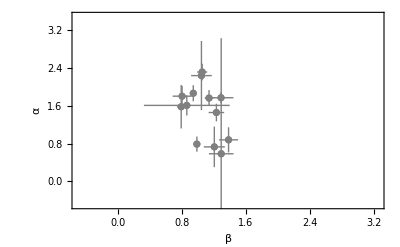

```mathematica
fullrelation=ListPlot[fullabplot,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Gray];
Show[fullrelation,PlotRange->{{-0.5,3.25},{-0.5,3.5}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β","All GRBs"}}]
```

```mathematica
rawdata[[1]]
```

{GRB_NAME,GBM_ID,OPT,OPT_beta,XRT,GBM,LAT,z,AG_temp_decay_model,BPL_temp_ind1,BPL_temp_ind1_err,BPL_temp_ind2,BPL_temp_ind2_err,SPL_temp_ind1,SPL_temp_ind1_err,LAT_spec_ind,LAT_spec_err_ind}

```mathematica
(* Indices *)
k=0;
total={};
bplTotal={};
splTotal={};

GreaterBPL={};
SlowLesser={};
SlowBetween={};
FastLesser={};
FastBetween={};
(* Plot points *)
(* Total *)
plotGreaterTot={};
plotGreaterTotErr={};
plotSlowLesserTot={};
plotSlowLesserTotErr={};
plotSlowBetweenTot={};
plotSlowBetweenTotErr={};
plotFastLesserTot={};
plotFastLesserTotErr={};
plotFastBetweenTot={};
plotFastBetweenTotErr={};

(* BPL *)
plotGreaterBPL={};
plotGreaterBPLErr={};
plotSlowLesserBPL={};
plotSlowLesserBPLErr={};
plotSlowBetweenBPL={};
plotSlowBetweenBPLErr={};
plotFastLesserBPL={};
plotFastLesserBPLErr={};
plotFastBetweenBPL={};
plotFastBetweenBPLErr={};

(* SPL *)
GreaterSPL={};
LesserSPL={};
SlowBetweenSPL={};
FastLesserSPL={};
FastBetweenSPL={};

(* Plot points *)
plotGreaterSPL={};
plotGreaterSPLErr={};
plotSlowLesserSPL={};
plotSlowLesserSPLErr={};
plotSlowBetweenSPL={};
plotSlowBetweenSPLErr={};
plotFastLesserSPL={};
plotFastLesserSPLErr={};
plotFastBetweenSPL={};
plotFastBetweenSPLErr={};

plotTotal={};
plotTotalErr={};
plotTotalBPL={};
plotTotalBPLErr={};
plotTotalSPL={};
plotTotalSPLErr={};

GRBsGreaterSPL={};
GRBsSlowLesserSPL={};
GRBsSlowBetweenSPL={};
GRBsFastLesserSPL={};
GRBsFastBetweenSPL={};

GRBsGreaterBPL={};
GRBsSlowLesserBPL={};
GRBsSlowBetweenBPL={};
GRBsFastLesserBPL={};
GRBsFastBetweenBPL={};


totalsample = {};

(*Relationships taken from Table 1 of Srinivasaragavan*)
Do[
z = sigdata[[i,8]];
alpha=sigdata[[i,12]];
alpha2 = sigdata[[i,10]];
beta=-1*sigdata[[i,16]] -1;
aErr = sigdata[[i,11]];
aErr2 = sigdata[[i,13]];
bErr = sigdata[[i,17]];
If[alpha2*beta*aErr2*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[bplTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha2-aErr2},{beta+bErr,alpha2+aErr2}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha2)^2/(aErr2)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha2-aErr2-0.1,alpha2+aErr2+0.1}}];

AppendTo[plotTotalBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
(*AppendTo[totalsample, {"idGRB", "z", "alpha", "alphaErr", "beta", "betaErr", "PL"}]*);
(*AppendTo[totalsample, {idGRB, z, alpha2, aErr2, beta, bErr, "BPL"}];*)
AppendTo[plotTotalBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];

(*(*ISM Slow Cooling, v < Subscript[v, m]*)(*ignored*)
r1=ImplicitRegion[(3*x)/2==y,{{x,-1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[ismSlowLesser,i];
AppendTo[plotIsmSlowLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotIsmSlowLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotIsmSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
];*)

(* v > Subscript[v, c],Subscript[v, m]*)
r1=ImplicitRegion[(3*x-1)/2==y,{{x,1,5},y}];
r2=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterBPL,i];
AppendTo[plotGreaterBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotGreaterBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsGreaterBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+9/4/(4-k)==y,{{x,0,0.5},y}];
r2=ImplicitRegion[3*x/2+k/2/(4-k)==y,{{x,0.5,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetween,i];
AppendTo[plotSlowBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotSlowBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsSlowBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[x/2==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesser,i];
AppendTo[plotFastLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotFastLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsFastLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
AppendTo[FastBetween,i];
AppendTo[plotFastBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotFastBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsFastBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];


(* SPL *)
,If[alpha*beta*aErr*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[splTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha)^2/(aErr)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha-aErr-0.1,alpha+aErr+0.1}}];

AppendTo[plotTotalSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
(*AppendTo[totalsample, {idGRB, z, alpha, aErr, beta, bErr, "SPL"}];*)
AppendTo[plotTotalSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];

(*(*ISM Slow Cooling, v < Subscript[v, m]*)
r1=ImplicitRegion[(3*x)/2==y,{{x,-1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[ismSlowLesserSPL,i];
AppendTo[plotIsmSlowLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotIsmSlowLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotIsmSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
];*)

(* v > Subscript[v, c], Subscript[v, m]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];
r2=ImplicitRegion[(3*x-1)/2==y,{{x,1,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterSPL,i];
AppendTo[plotGreaterSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotGreaterSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsGreaterSPL, idGRB];
AppendTo[totalsample, idGRB];

];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+9/4/(4-k)==y,{{x,0,0.5},y}];
r2=ImplicitRegion[3*x/2+k/2/(4-k)==y,{{x,0.5,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetweenSPL,i];
AppendTo[plotSlowBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, v < Subscript[v, c], Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[x/2==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesserSPL,i];
AppendTo[plotFastLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
AppendTo[FastBetweenSPL,i];
AppendTo[plotFastBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];


]
],{i,1,Length[sigdata]}];
```

```mathematica
nototalsamplek0 = DeleteDuplicates[totalsample]
```

{idGRB}

Select::normal: Nonatomic expression expected at position 1 in Select[displayData,#1⟦11⟧ #1⟦3⟧≠0.&].

```mathematica
GRBsGreaterSPL
GRBsSlowLesserSPL
GRBsSlowBetweenSPL
GRBsFastLesserSPL
GRBsFastBetweenSPL

GRBsGreaterBPL
GRBsSlowLesserBPL
GRBsSlowBetweenBPL
GRBsFastLesserBPL
GRBsFastBetweenBPL
```

{}

{}

{}

«2 more identical outputs»

{idGRB,idGRB,idGRB}

{}

{idGRB,idGRB,idGRB,idGRB}

{}

{}

Total Number of GRBs considered: 13

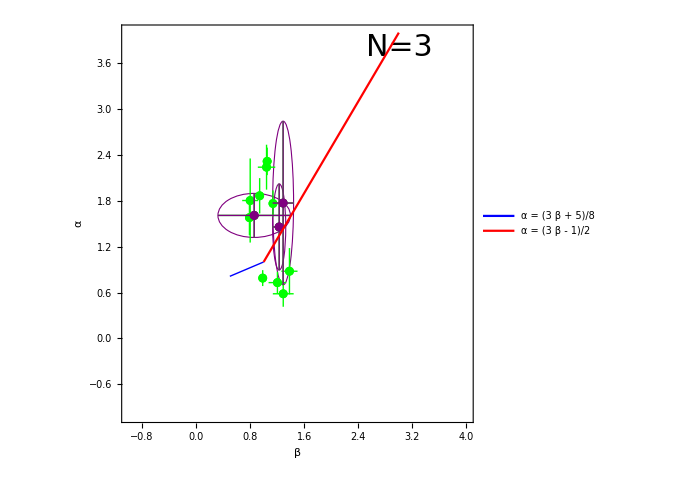

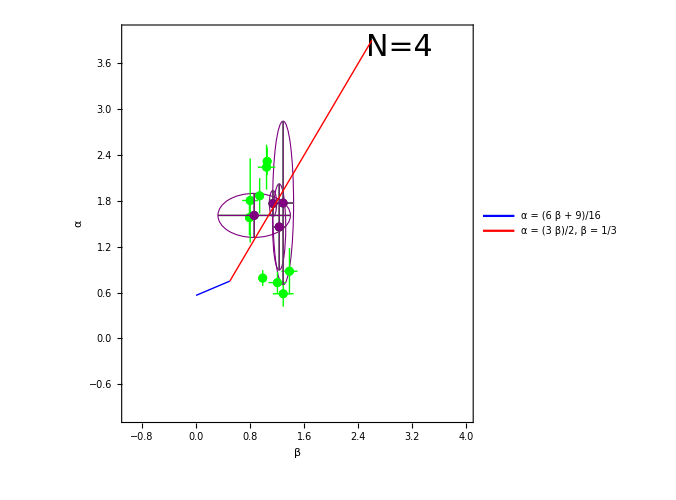

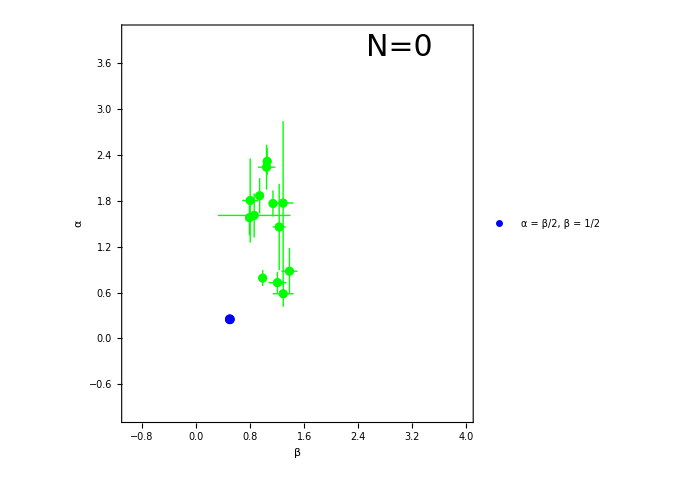

```mathematica
(*Plots*)
"Total Number of GRBs considered: "<>ToString[Length[total]]
splplot=ListPlot[{}];
totalplot=ListPlot[plotTotal,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
bplplot=ListPlot[plotTotalBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotTotalSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];

all={};

satbplplot=ListPlot[plotGreaterBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotGreaterSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[GreaterBPL]+Length[GreaterSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+(5-k)/2/(4-k)},{x,0.5,1.0},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Directive[Blue, Thick]},PlotLegends->Placed[{"α = (3  β + 5)/8"},{0.75,0.8}]]];
reg2=With[{t=.0004,d=.5,background=White},Plot[{(3*x-1)/2},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = (3  β - 1)/2"},{0.75,0.65}]]];
Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"Greater.pdf",Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->23.5,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
AppendTo[all,reg2];



satbplplot=ListPlot[plotSlowBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+9/4/(4-k)},{x,0,0.5},PlotStyle->{Directive[Blue, Thick]},PlotLegends->Placed[{"α = (6  β + 9)/16"},{0.7,0.8}]]];

If[k==0,
reg2=With[{t=.0004,d=.5,background=White},Plot[{3*x/2+k/2/(4-k)},{x, 0.5, 2.6},PlotStyle->{Directive[Red, Thick]},PlotLegends->Placed[{"α = (3  β)/2, β = 1/3"},{0.7,0.65}]]]
];

Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"SlowBetween.pdf",Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->22,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
AppendTo[all,reg2];




satbplplot=ListPlot[plotFastBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastBetween]+Length[FastBetweenSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
basereg=ListPlot[{{0.5,0.25}},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}, PlotLegends->Placed[{"α = β/2, β = 1/2"},{0.7,0.8}]];
Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,basereg,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"FastBetween.pdf",Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,basereg,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->22,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,basereg];
```

```mathematica
summary={{"k","Cooling","v Range","CR: 1 < p < 2","CR: p > 2","GRBs Satisfying Relation","Proportion Satisfying Relation"},
(*{"ISM","Slow","v < v_m",   "[3β/2]",     ToString[Length[ismSlowLesser]+Length[ismSlowLesserSPL]],          ToString[DecimalForm[100.*(Length[ismSlowLesser]+Length[ismSlowLesserSPL])/Length[total],3]]<>"%"},*)
{ToString[k],"Slow","v_m < v < v_c","α=("<>ToString[2*(3-k)]<>"β+9)/"<>ToString[4*(4-k)],If[k==0,"α=3β/2","α=("<>ToString[3*(4-k)]<>"β+"<>ToString[k]<>")/"<>ToString[2*(4-k)]],ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],ToString[DecimalForm[100.*(Length[SlowBetween]+Length[SlowBetweenSPL])/Length[total],3]]<>"%"},
{ToString[k],"","v > v_c,v_m","α=("<>ToString[3-k]<>"β+"<>ToString[5-k]<>")/"<>ToString[2*(4-k)],"(3β-1)/2",ToString[Length[GreaterBPL]+Length[GreaterSPL]],     ToString[DecimalForm[100.*(Length[GreaterBPL]+Length[GreaterSPL])/Length[total],3]]<>"%"},
(*{"ISM","Fast","v < v_c",   "[β/2]",        ToString[Length[ismFastLesser]+Length[ismFastLesserSPL]],          ToString[DecimalForm[100.*(Length[ismFastLesser]+Length[ismFastLesserSPL])/Length[total],3]]<>"%"},*)
{ToString[k],"Fast","v_c < v < v_m","β/2","β/2",ToString[Length[FastBetween]+Length[FastBetweenSPL]],ToString[DecimalForm[100.*(Length[FastBetween]+Length[FastBetweenSPL])/Length[total],3]]<>"%"}
};
"Total Number of GRBs: " <> ToString[Length[total]]
TableForm[Rest[summary],TableHeadings->{None,summary[[1,All]]}]
```

Total Number of GRBs: 13

k | Cooling | v Range | CR: 1 < p < 2 | CR: p > 2 | GRBs Satisfying Relation | Proportion Satisfying Relation
0 | Slow | v_m < v < v_c | α=(6β+9)/16 | α=3β/2 | 4 | 30.8%
0 |  | v > v_c,v_m | α=(3β+5)/8 | (3β-1)/2 | 3 | 23.1%
0 | Fast | v_c < v < v_m | β/2 | β/2 | 0 | 0.%

```mathematica
K = 1
```

1

```mathematica
k=1;
total={};
bplTotal={};
splTotal={};

GreaterBPL={};
SlowLesser={};
SlowBetween={};
FastLesser={};
FastBetween={};
(* Plot points *)
(* Total *)
plotGreaterTot={};
plotGreaterTotErr={};
plotSlowLesserTot={};
plotSlowLesserTotErr={};
plotSlowBetweenTot={};
plotSlowBetweenTotErr={};
plotFastLesserTot={};
plotFastLesserTotErr={};
plotFastBetweenTot={};
plotFastBetweenTotErr={};

(* BPL *)
plotGreaterBPL={};
plotGreaterBPLErr={};
plotSlowLesserBPL={};
plotSlowLesserBPLErr={};
plotSlowBetweenBPL={};
plotSlowBetweenBPLErr={};
plotFastLesserBPL={};
plotFastLesserBPLErr={};
plotFastBetweenBPL={};
plotFastBetweenBPLErr={};

(* SPL *)
GreaterSPL={};
LesserSPL={};
SlowBetweenSPL={};
FastLesserSPL={};
FastBetweenSPL={};

(* Plot points *)
plotGreaterSPL={};
plotGreaterSPLErr={};
plotSlowLesserSPL={};
plotSlowLesserSPLErr={};
plotSlowBetweenSPL={};
plotSlowBetweenSPLErr={};
plotFastLesserSPL={};
plotFastLesserSPLErr={};
plotFastBetweenSPL={};
plotFastBetweenSPLErr={};

plotTotal={};
plotTotalErr={};
plotTotalBPL={};
plotTotalBPLErr={};
plotTotalSPL={};
plotTotalSPLErr={};

GRBsGreaterSPL={};
GRBsSlowLesserSPL={};
GRBsSlowBetweenSPL={};
GRBsFastLesserSPL={};
GRBsFastBetweenSPL={};

GRBsGreaterBPL={};
GRBsSlowLesserBPL={};
GRBsSlowBetweenBPL={};
GRBsFastLesserBPL={};
GRBsFastBetweenBPL={};


totalsample = {};
(*Relationships taken from Table 1 of Srinivasaragavan*)
Do[
idGRB = sigdata[[i, 1]]; 
z = sigdata[[i, 8]]; 
alpha2=sigdata[[i,12]];
alpha=sigdata[[i,10]];
beta=-1*sigdata[[i,16]] -1;
aErr2 = sigdata[[i,13]];
aErr=sigdata[[i,11]];
bErr = sigdata[[i,17]];

If[alpha2*beta*aErr2*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[bplTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha2-aErr2},{beta+bErr,alpha2+aErr2}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha2)^2/(aErr2)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha2-aErr2-0.1,alpha2+aErr2+0.1}}];

AppendTo[plotTotalBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
(*AppendTo[totalsample, {"idGRB", "z", "alpha", "alphaErr", "beta", "betaErr", "PL"}]*);
(*AppendTo[totalsample, {idGRB, z, alpha2, aErr2, beta, bErr, "BPL"}];*)
AppendTo[plotTotalBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];

(*(*ISM Slow Cooling, v < Subscript[v, m]*)(*ignored*)
r1=ImplicitRegion[(3*x)/2==y,{{x,-1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[ismSlowLesser,i];
AppendTo[plotIsmSlowLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotIsmSlowLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotIsmSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
];*)

(* v > Subscript[v, c],Subscript[v, m]*)
r1=ImplicitRegion[(3*x-1)/2==y,{{x,1,5},y}];
r2=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterBPL,i];
AppendTo[plotGreaterBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotGreaterBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsGreaterBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+9/4/(4-k)==y,{{x,0,0.5},y}];
r2=ImplicitRegion[3*x/2+k/2/(4-k)==y,{{x,0.5,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetween,i];
AppendTo[plotSlowBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotSlowBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsSlowBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[x/2==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesser,i];
AppendTo[plotFastLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotFastLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsFastLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
AppendTo[FastBetween,i];
AppendTo[plotFastBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotFastBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsFastBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];


(* SPL *)
,If[alpha*beta*aErr*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[splTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha)^2/(aErr)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha-aErr-0.1,alpha+aErr+0.1}}];

AppendTo[plotTotalSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
(*AppendTo[totalsample, {idGRB, z, alpha, aErr, beta, bErr, "SPL"}];*)
AppendTo[plotTotalSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];

(*(*ISM Slow Cooling, v < Subscript[v, m]*)
r1=ImplicitRegion[(3*x)/2==y,{{x,-1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[ismSlowLesserSPL,i];
AppendTo[plotIsmSlowLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotIsmSlowLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotIsmSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
];*)

(* v > Subscript[v, c], Subscript[v, m]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];
r2=ImplicitRegion[(3*x-1)/2==y,{{x,1,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterSPL,i];
AppendTo[plotGreaterSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotGreaterSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsGreaterSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+9/4/(4-k)==y,{{x,0,0.5},y}];
r2=ImplicitRegion[3*x/2+k/2/(4-k)==y,{{x,0.5,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetweenSPL,i];
AppendTo[plotSlowBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, v < Subscript[v, c], Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[x/2==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesserSPL,i];
AppendTo[plotFastLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[FastBetweenSPL,i];
AppendTo[GRBsFastLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
AppendTo[plotFastBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];


]
],{i,1,Length[sigdata]}];
```

```mathematica
noactualtotalk1= DeleteDuplicates[totalsample]
```

{080916C,110731A,221009A,171010A,090926A,160509A}

```mathematica
GRBsGreaterSPL
GRBsSlowLesserSPL
GRBsSlowBetweenSPL
GRBsFastLesserSPL
GRBsFastBetweenSPL

GRBsGreaterBPL
GRBsSlowLesserBPL
GRBsSlowBetweenBPL
GRBsFastLesserBPL
GRBsFastBetweenBPL
```

{}

{}

{}

«2 more identical outputs»

{110731A,221009A,171010A,090926A,160509A}

{}

{}

{080916C}

{080916C}

Total Number of GRBs considered: 13

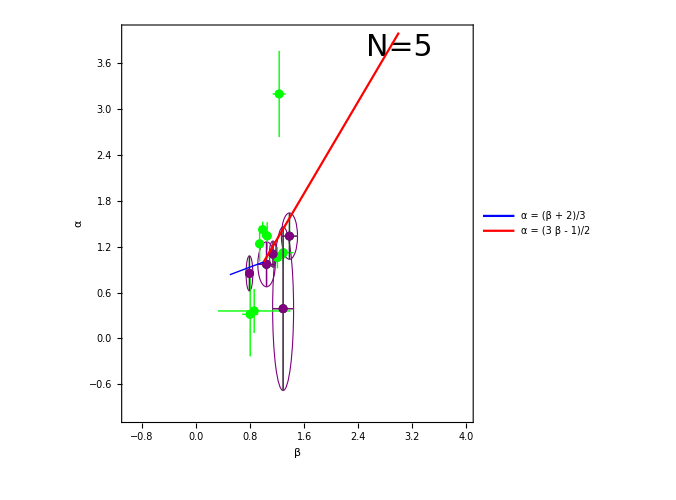

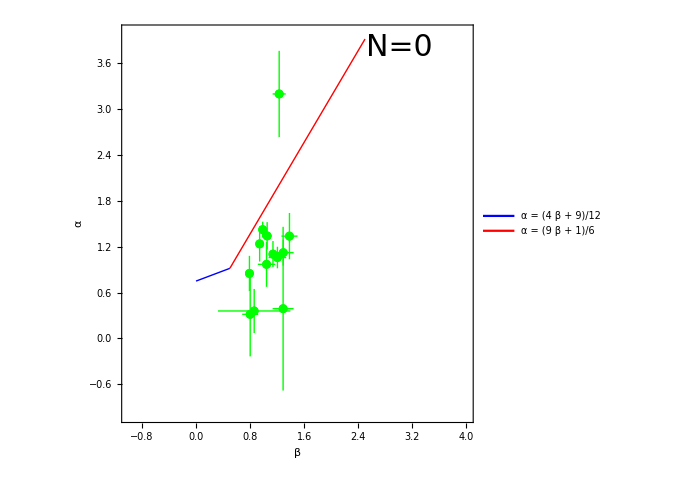

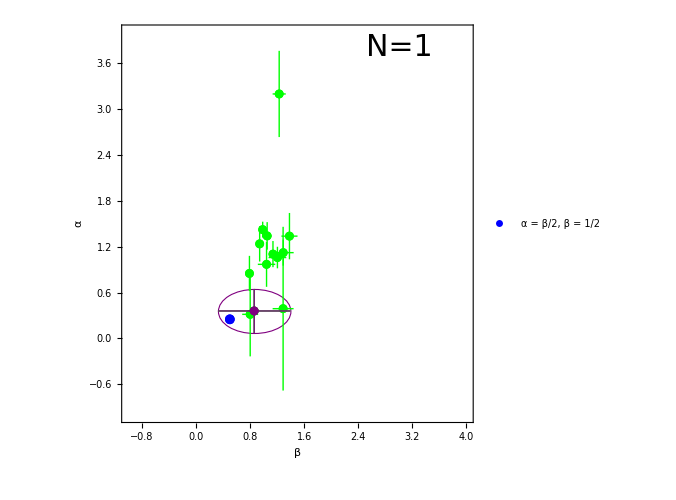

```mathematica
(*Plots*)
"Total Number of GRBs considered: "<>ToString[Length[total]]
splplot=ListPlot[{}];
totalplot=ListPlot[plotTotal,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
bplplot=ListPlot[plotTotalBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotTotalSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];

all={};

(**bplplot=ListPlot[plotIsmSlowGreater,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotIsmSlowGreaterSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];*)
satbplplot=ListPlot[plotGreaterBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotGreaterSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[GreaterBPL]+Length[GreaterSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+(5-k)/2/(4-k)},{x,0.5,1.0},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Directive[Blue, Thick]},PlotLegends->Placed[{"α = (β + 2)/3"},{0.7,0.8}]]];
reg2=With[{t=.0004,d=.5,background=White},Plot[{(3*x-1)/2},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = (3  β - 1)/2"},{0.7,0.65}]]];
(*Show[txt,bplplot,splplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β","GRBS with k = "<>ToString[k]<>", v > v_c,v_m"}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Show[txt,bplplot,splplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]*)
Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"Greater.pdf",Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
AppendTo[all,reg2];


(*bplplot=ListPlot[plotIsmSlowBetween,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotIsmSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];*)
satbplplot=ListPlot[plotSlowBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
(*reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+9/4/(4-k)},{x,0.0,0.5},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Blue},PlotLegends->Placed[{"α=("<>ToString[2*(3-k)]<>"β+9)/"<>ToString[4*(4-k)]},{0.8,0.8}]]];*)
reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+9/4/(4-k)},{x, 0, 0.5},PlotStyle->{Directive[Blue, Thick]},PlotLegends->Placed[{"α = (4  β + 9)/12"},{0.65,0.8}]]];
reg2=With[{t=.0004,d=.5,background=White},Plot[{3*x/2+k/2/(4-k)},{x, 0.5, 2.5},PlotStyle->{Directive[Red, Thick]},PlotLegends->Placed[{"α = (9  β + 1)/6"},{0.65,0.65}]]];

Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"SlowBetween.pdf",Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
AppendTo[all,reg2];


satbplplot=ListPlot[plotFastBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastBetween]+Length[FastBetweenSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
basereg=ListPlot[{{0.5,0.25}},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}, PlotLegends->Placed[{"α = β/2, β = 1/2"},{0.7,0.8}]];
Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,basereg,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"FastBetween.pdf",Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,basereg,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,basereg];
```

```mathematica
summary={{"k","Cooling","v Range","CR: 1 < p < 2","CR: p > 2","GRBs Satisfying Relation","Proportion Satisfying Relation"},
(*{"ISM","Slow","v < v_m",   "[3β/2]",     ToString[Length[ismSlowLesser]+Length[ismSlowLesserSPL]],          ToString[DecimalForm[100.*(Length[ismSlowLesser]+Length[ismSlowLesserSPL])/Length[total],3]]<>"%"},*)
{ToString[k],"Slow","v_m < v < v_c","α=("<>ToString[2*(3-k)]<>"β+9)/"<>ToString[4*(4-k)],If[k==0,"α=3β/2","α=("<>ToString[3*(4-k)]<>"β+"<>ToString[k]<>")/"<>ToString[2*(4-k)]],ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],ToString[DecimalForm[100.*(Length[SlowBetween]+Length[SlowBetweenSPL])/Length[total],3]]<>"%"},
{ToString[k],"","v > v_c,v_m","α=("<>ToString[3-k]<>"β+"<>ToString[5-k]<>")/"<>ToString[2*(4-k)],"(3β-1)/2",ToString[Length[GreaterBPL]+Length[GreaterSPL]],     ToString[DecimalForm[100.*(Length[GreaterBPL]+Length[GreaterSPL])/Length[total],3]]<>"%"},
(*{"ISM","Fast","v < v_c",   "[β/2]",        ToString[Length[ismFastLesser]+Length[ismFastLesserSPL]],          ToString[DecimalForm[100.*(Length[ismFastLesser]+Length[ismFastLesserSPL])/Length[total],3]]<>"%"},*)
{ToString[k],"Fast","v_c < v < v_m","β/2","β/2",ToString[Length[FastBetween]+Length[FastBetweenSPL]],ToString[DecimalForm[100.*(Length[FastBetween]+Length[FastBetweenSPL])/Length[total],3]]<>"%"}
};
"Total Number of GRBs: " <> ToString[Length[total]]
TableForm[Rest[summary],TableHeadings->{None,summary[[1,All]]}]
```

Total Number of GRBs: 13

k | Cooling | v Range | CR: 1 < p < 2 | CR: p > 2 | GRBs Satisfying Relation | Proportion Satisfying Relation
1 | Slow | v_m < v < v_c | α=(4β+9)/12 | α=(9β+1)/6 | 0 | 0.%
1 |  | v > v_c,v_m | α=(2β+4)/6 | (3β-1)/2 | 5 | 38.5%
1 | Fast | v_c < v < v_m | β/2 | β/2 | 1 | 7.69%

```mathematica
K = 1.5 CASE
```

1.5 CASE

```mathematica
k=1.5;
total={};
bplTotal={};
splTotal={};

GreaterBPL={};
SlowLesser={};
SlowBetween={};
FastLesser={};
FastBetween={};
(* Plot points *)
(* Total *)
plotGreaterTot={};
plotGreaterTotErr={};
plotSlowLesserTot={};
plotSlowLesserTotErr={};
plotSlowBetweenTot={};
plotSlowBetweenTotErr={};
plotFastLesserTot={};
plotFastLesserTotErr={};
plotFastBetweenTot={};
plotFastBetweenTotErr={};

(* BPL *)
plotGreaterBPL={};
plotGreaterBPLErr={};
plotSlowLesserBPL={};
plotSlowLesserBPLErr={};
plotSlowBetweenBPL={};
plotSlowBetweenBPLErr={};
plotFastLesserBPL={};
plotFastLesserBPLErr={};
plotFastBetweenBPL={};
plotFastBetweenBPLErr={};

(* SPL *)
GreaterSPL={};
LesserSPL={};
SlowBetweenSPL={};
FastLesserSPL={};
FastBetweenSPL={};

(* Plot points *)
plotGreaterSPL={};
plotGreaterSPLErr={};
plotSlowLesserSPL={};
plotSlowLesserSPLErr={};
plotSlowBetweenSPL={};
plotSlowBetweenSPLErr={};
plotFastLesserSPL={};
plotFastLesserSPLErr={};
plotFastBetweenSPL={};
plotFastBetweenSPLErr={};

plotTotal={};
plotTotalErr={};
plotTotalBPL={};
plotTotalBPLErr={};
plotTotalSPL={};
plotTotalSPLErr={};

GRBsGreaterSPL={};
GRBsSlowLesserSPL={};
GRBsSlowBetweenSPL={};
GRBsFastLesserSPL={};
GRBsFastBetweenSPL={};

GRBsGreaterBPL={};
GRBsSlowLesserBPL={};
GRBsSlowBetweenBPL={};
GRBsFastLesserBPL={};
GRBsFastBetweenBPL={};

totalsample = {};
(*Relationships taken from Table 1 of Srinivasaragavan*)
Do[
idGRB = sigdata[[i, 1]]; 
z = sigdata[[i, 8]]; 
alpha2=sigdata[[i,12]];
alpha=sigdata[[i,10]];
beta=-1*sigdata[[i,16]] -1;
aErr2 = sigdata[[i,13]];
aErr=sigdata[[i,11]];
bErr = sigdata[[i,17]];

If[alpha2*beta*aErr2*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[bplTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha2-aErr2},{beta+bErr,alpha2+aErr2}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha2)^2/(aErr2)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha2-aErr2-0.1,alpha2+aErr2+0.1}}];

AppendTo[plotTotalBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
(*AppendTo[totalsample, {"idGRB", "z", "alpha", "alphaErr", "beta", "betaErr", "PL"}]*);
(*AppendTo[totalsample, {idGRB, z, alpha2, aErr2, beta, bErr, "BPL"}];*)
AppendTo[plotTotalBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];

(*(*ISM Slow Cooling, v < Subscript[v, m]*)(*ignored*)
r1=ImplicitRegion[(3*x)/2==y,{{x,-1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[ismSlowLesser,i];
AppendTo[plotIsmSlowLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotIsmSlowLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotIsmSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
];*)

(* v > Subscript[v, c],Subscript[v, m]*)
r1=ImplicitRegion[(3*x-1)/2==y,{{x,1,5},y}];
r2=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterBPL,i];
AppendTo[plotGreaterBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotGreaterBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsGreaterBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+9/4/(4-k)==y,{{x,0,0.5},y}];
r2=ImplicitRegion[3*x/2+k/2/(4-k)==y,{{x,0.5,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetween,i];
AppendTo[plotSlowBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotSlowBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsSlowBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[x/2==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesser,i];
AppendTo[plotFastLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotFastLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsFastLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
AppendTo[FastBetween,i];
AppendTo[plotFastBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotFastBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsFastBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];


(* SPL *)
,If[alpha*beta*aErr*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[splTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha)^2/(aErr)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha-aErr-0.1,alpha+aErr+0.1}}];

AppendTo[plotTotalSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
(*AppendTo[totalsample, {idGRB, z, alpha, aErr, beta, bErr, "SPL"}];*)
AppendTo[plotTotalSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];

(*(*ISM Slow Cooling, v < Subscript[v, m]*)
r1=ImplicitRegion[(3*x)/2==y,{{x,-1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[ismSlowLesserSPL,i];
AppendTo[plotIsmSlowLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotIsmSlowLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotIsmSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
];*)

(* v > Subscript[v, c], Subscript[v, m]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];
r2=ImplicitRegion[(3*x-1)/2==y,{{x,1,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterSPL,i];
AppendTo[plotGreaterSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotGreaterSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsGreaterSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+9/4/(4-k)==y,{{x,0,0.5},y}];
r2=ImplicitRegion[3*x/2+k/2/(4-k)==y,{{x,0.5,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetweenSPL,i];
AppendTo[plotSlowBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, v < Subscript[v, c], Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[x/2==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesserSPL,i];
AppendTo[plotFastLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
AppendTo[FastBetweenSPL,i];
AppendTo[plotFastBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];


]
],{i,1,Length[sigdata]}];
```

```mathematica
noactualtotalk15 = DeleteDuplicates[totalsample]
```

{080916C,110731A,221009A,171010A,090926A,160509A}

```mathematica
GRBsGreaterSPL
GRBsSlowLesserSPL
GRBsSlowBetweenSPL
GRBsFastLesserSPL
GRBsFastBetweenSPL

GRBsGreaterBPL
GRBsSlowLesserBPL
GRBsSlowBetweenBPL
GRBsFastLesserBPL
GRBsFastBetweenBPL
```

{}

{}

{}

«2 more identical outputs»

{110731A,221009A,171010A,090926A,160509A}

{}

{}

{080916C}

{080916C}

Total Number of GRBs considered: 13

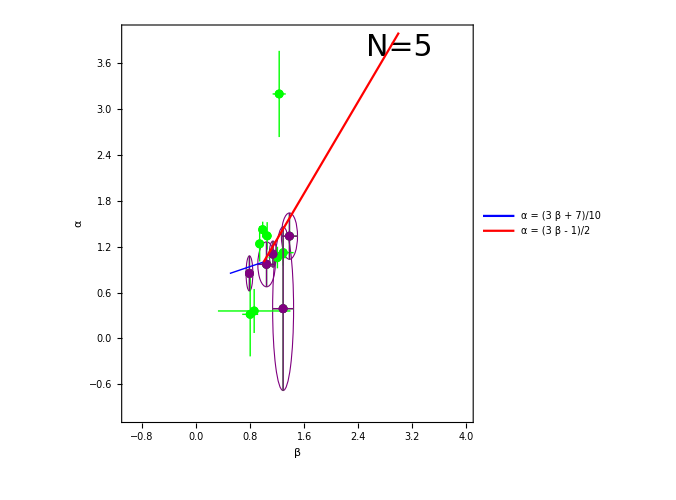

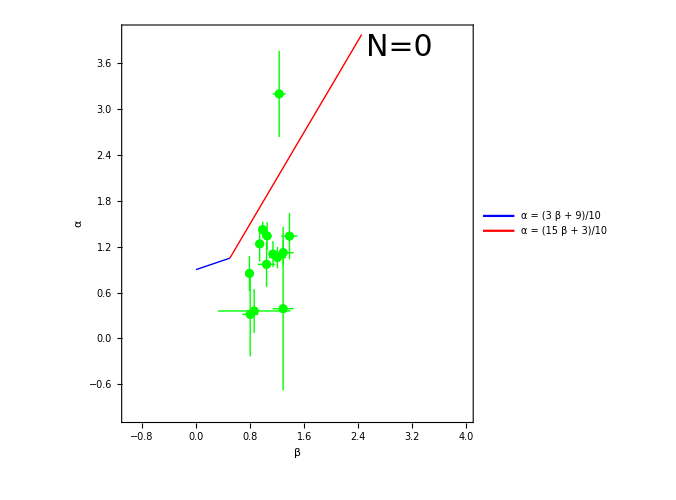

-Graphics-

```mathematica
(*Plots*)
"Total Number of GRBs considered: "<>ToString[Length[total]]
splplot=ListPlot[{}];
totalplot=ListPlot[plotTotal,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
bplplot=ListPlot[plotTotalBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotTotalSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];

all={};


satbplplot=ListPlot[plotGreaterBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotGreaterSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[GreaterBPL]+Length[GreaterSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+(5-k)/2/(4-k)},{x,0.5,1.0},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Directive[Blue, Thick]},PlotLegends->Placed[{"α = (3  β + 7)/10"},{0.7,0.8}]]];
reg2=With[{t=.0004,d=.5,background=White},Plot[{(3*x-1)/2},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = (3  β - 1)/2"},{0.7,0.65}]]];
Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"Greater.pdf",Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
AppendTo[all,reg2];



satbplplot=ListPlot[plotSlowBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+9/4/(4-k)},{x, 0, 0.5}, PlotStyle->{Directive[Blue, Thick]}, PlotLegends->Placed[{"α = (3  β + 9)/10"},{0.65,0.8}]]];
reg2=With[{t=.0004,d=.5,background=White},Plot[{3*x/2+k/2/(4-k)},{x, 0.5, 2.45},PlotStyle->{Directive[Red, Thick]},PlotLegends->Placed[{"α = (15  β + 3)/10"},{0.65,0.65}]]];
Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"SlowBetween.pdf",Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
AppendTo[all,reg2];


satbplplot=ListPlot[plotFastBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastBetween]+Length[FastBetweenSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
basereg=ListPlot[{{0.5,0.25}},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}, PlotLegends->Placed[{"α = β/2, β = 1/2"},{0.7,0.8}]];
Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,basereg,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"FastBetween.pdf",Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,basereg,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,basereg];
```

```mathematica
summary={{"k","Cooling","v Range","CR: 1 < p < 2","CR: p > 2","GRBs Satisfying Relation","Proportion Satisfying Relation"},
(*{"ISM","Slow","v < v_m",   "[3β/2]",     ToString[Length[ismSlowLesser]+Length[ismSlowLesserSPL]],          ToString[DecimalForm[100.*(Length[ismSlowLesser]+Length[ismSlowLesserSPL])/Length[total],3]]<>"%"},*)
{ToString[k],"Slow","v_m < v < v_c","α=("<>ToString[2*(3-k)]<>"β+9)/"<>ToString[4*(4-k)],If[k==0,"α=3β/2","α=("<>ToString[3*(4-k)]<>"β+"<>ToString[k]<>")/"<>ToString[2*(4-k)]],ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],ToString[DecimalForm[100.*(Length[SlowBetween]+Length[SlowBetweenSPL])/Length[total],3]]<>"%"},
{ToString[k],"","v > v_c,v_m","α=("<>ToString[3-k]<>"β+"<>ToString[5-k]<>")/"<>ToString[2*(4-k)],"(3β-1)/2",ToString[Length[GreaterBPL]+Length[GreaterSPL]],     ToString[DecimalForm[100.*(Length[GreaterBPL]+Length[GreaterSPL])/Length[total],3]]<>"%"},
(*{"ISM","Fast","v < v_c",   "[β/2]",        ToString[Length[ismFastLesser]+Length[ismFastLesserSPL]],          ToString[DecimalForm[100.*(Length[ismFastLesser]+Length[ismFastLesserSPL])/Length[total],3]]<>"%"},*)
{ToString[k],"Fast","v_c < v < v_m","β/2","β/2",ToString[Length[FastBetween]+Length[FastBetweenSPL]],ToString[DecimalForm[100.*(Length[FastBetween]+Length[FastBetweenSPL])/Length[total],3]]<>"%"}
};
"Total Number of GRBs: " <> ToString[Length[total]]
TableForm[Rest[summary],TableHeadings->{None,summary[[1,All]]}]
```

Total Number of GRBs: 13

k | Cooling | v Range | CR: 1 < p < 2 | CR: p > 2 | GRBs Satisfying Relation | Proportion Satisfying Relation
1.5 | Slow | v_m < v < v_c | α=(3.β+9)/10. | α=(7.5β+1.5)/5. | 0 | 0.%
1.5 |  | v > v_c,v_m | α=(1.5β+3.5)/5. | (3β-1)/2 | 5 | 38.5%
1.5 | Fast | v_c < v < v_m | β/2 | β/2 | 1 | 7.69%

```mathematica
K =2
```

2

```mathematica
k=2;
total={};
bplTotal={};
splTotal={};

GreaterBPL={};
SlowLesser={};
SlowBetween={};
FastLesser={};
FastBetween={};
(* Plot points *)
(* Total *)
plotGreaterTot={};
plotGreaterTotErr={};
plotSlowLesserTot={};
plotSlowLesserTotErr={};
plotSlowBetweenTot={};
plotSlowBetweenTotErr={};
plotFastLesserTot={};
plotFastLesserTotErr={};
plotFastBetweenTot={};
plotFastBetweenTotErr={};

(* BPL *)
plotGreaterBPL={};
plotGreaterBPLErr={};
plotSlowLesserBPL={};
plotSlowLesserBPLErr={};
plotSlowBetweenBPL={};
plotSlowBetweenBPLErr={};
plotFastLesserBPL={};
plotFastLesserBPLErr={};
plotFastBetweenBPL={};
plotFastBetweenBPLErr={};

(* SPL *)
GreaterSPL={};
LesserSPL={};
SlowBetweenSPL={};
FastLesserSPL={};
FastBetweenSPL={};

(* Plot points *)
plotGreaterSPL={};
plotGreaterSPLErr={};
plotSlowLesserSPL={};
plotSlowLesserSPLErr={};
plotSlowBetweenSPL={};
plotSlowBetweenSPLErr={};
plotFastLesserSPL={};
plotFastLesserSPLErr={};
plotFastBetweenSPL={};
plotFastBetweenSPLErr={};

plotTotal={};
plotTotalErr={};
plotTotalBPL={};
plotTotalBPLErr={};
plotTotalSPL={};
plotTotalSPLErr={};

GRBsGreaterSPL={};
GRBsSlowLesserSPL={};
GRBsSlowBetweenSPL={};
GRBsFastLesserSPL={};
GRBsFastBetweenSPL={};

GRBsGreaterBPL={};
GRBsSlowLesserBPL={};
GRBsSlowBetweenBPL={};
GRBsFastLesserBPL={};
GRBsFastBetweenBPL={};

totalsample = {};
(*Relationships taken from Table 1 of Srinivasaragavan*)
Do[
idGRB = sigdata[[i, 1]]; 
z = sigdata[[i, 8]]; 
alpha2=sigdata[[i,12]];
alpha=sigdata[[i,10]];
beta=-1*sigdata[[i,16]] -1;
aErr2 = sigdata[[i,13]];
aErr=sigdata[[i,11]];
bErr = sigdata[[i,17]];

If[alpha2*beta*aErr2*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[bplTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha2-aErr2},{beta+bErr,alpha2+aErr2}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha2)^2/(aErr2)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha2-aErr2-0.1,alpha2+aErr2+0.1}}];

AppendTo[plotTotalBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
(*AppendTo[totalsample, {"idGRB", "z", "alpha", "alphaErr", "beta", "betaErr", "PL"}]*);
(*AppendTo[totalsample, {idGRB, z, alpha2, aErr2, beta, bErr, "BPL"}];*)
AppendTo[plotTotalBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];

(*(*ISM Slow Cooling, v < Subscript[v, m]*)(*ignored*)
r1=ImplicitRegion[(3*x)/2==y,{{x,-1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[ismSlowLesser,i];
AppendTo[plotIsmSlowLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotIsmSlowLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotIsmSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
];*)

(* v > Subscript[v, c],Subscript[v, m]*)
r1=ImplicitRegion[(3*x-1)/2==y,{{x,1,5},y}];
r2=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterBPL,i];
AppendTo[plotGreaterBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotGreaterBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsGreaterBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+9/4/(4-k)==y,{{x,0.,0.5},y}];
r2=ImplicitRegion[3*x/2+k/2/(4-k)==y,{{x,0.5,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetween,i];
AppendTo[plotSlowBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotSlowBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsSlowBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[x/2==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesser,i];
AppendTo[plotFastLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotFastLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsFastLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
AppendTo[FastBetween,i];
AppendTo[plotFastBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotFastBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsFastBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];


(* SPL *)
,If[alpha*beta*aErr*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[splTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha)^2/(aErr)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha-aErr-0.1,alpha+aErr+0.1}}];

AppendTo[plotTotalSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
(*AppendTo[totalsample, {idGRB, z, alpha, aErr, beta, bErr, "SPL"}];*)
AppendTo[plotTotalSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];

(*(*ISM Slow Cooling, v < Subscript[v, m]*)
r1=ImplicitRegion[(3*x)/2==y,{{x,-1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[ismSlowLesserSPL,i];
AppendTo[plotIsmSlowLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotIsmSlowLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotIsmSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
];*)

(* v > Subscript[v, c], Subscript[v, m]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];
r2=ImplicitRegion[(3*x-1)/2==y,{{x,1,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterSPL,i];
AppendTo[plotGreaterSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotGreaterSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsGreaterSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+9/4/(4-k)==y,{{x,0,0.5},y}];
r2=ImplicitRegion[3*x/2+k/2/(4-k)==y,{{x,0.5,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetweenSPL,i];
AppendTo[plotSlowBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, v < Subscript[v, c], Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[x/2==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesserSPL,i];
AppendTo[plotFastLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
AppendTo[FastBetweenSPL,i];
AppendTo[plotFastBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];


]
],{i,1,Length[sigdata]}];
```

```mathematica
noactualtotalk2= DeleteDuplicates[totalsample]
```

{080916C,110731A,221009A,171010A,090926A,160509A}

```mathematica
GRBsGreaterSPL
GRBsSlowLesserSPL
GRBsSlowBetweenSPL
GRBsFastLesserSPL
GRBsFastBetweenSPL

GRBsGreaterBPL
GRBsSlowLesserBPL
GRBsSlowBetweenBPL
GRBsFastLesserBPL
GRBsFastBetweenBPL
```

{}

{}

{}

«2 more identical outputs»

{110731A,221009A,171010A,090926A,160509A}

{}

{}

{080916C}

{080916C}

Total Number of GRBs considered: 13

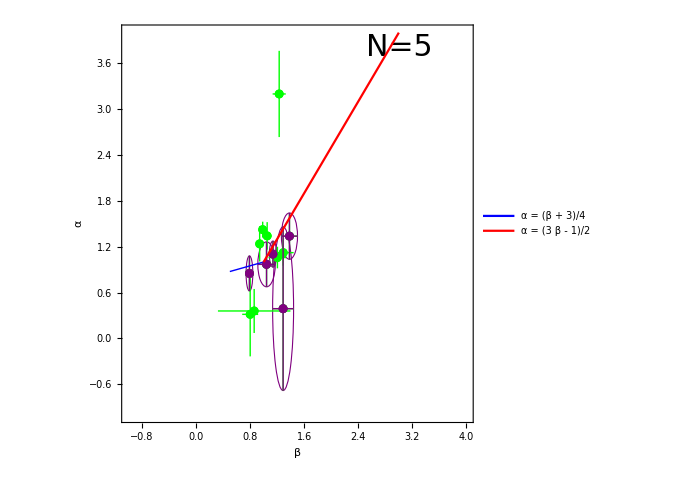

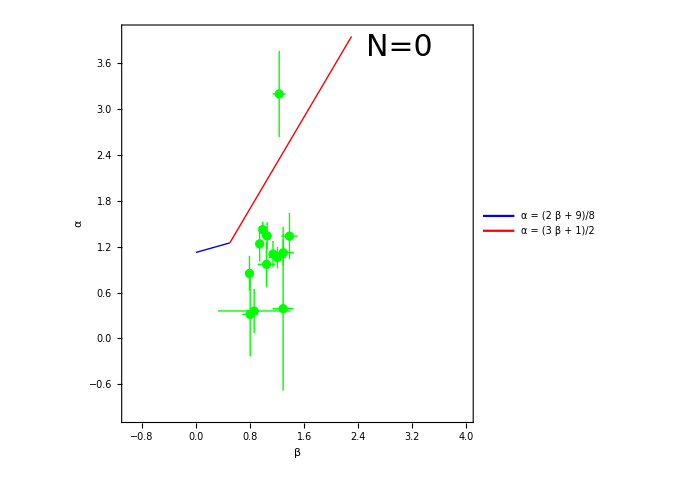

-Graphics-

```mathematica
(*Plots*)
"Total Number of GRBs considered: "<>ToString[Length[total]]
splplot=ListPlot[{}];
totalplot=ListPlot[plotTotal,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
bplplot=ListPlot[plotTotalBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotTotalSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];

all={};

satbplplot=ListPlot[plotGreaterBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotGreaterSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[GreaterBPL]+Length[GreaterSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+(5-k)/2/(4-k)},{x,0.5,1.0},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Directive[Blue, Thick]},PlotLegends->Placed[{"α = (β + 3)/4"},{0.7,0.8}]]];
reg2=With[{t=.0004,d=.5,background=White},Plot[{(3*x-1)/2},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = (3  β - 1)/2"},{0.7,0.65}]]];
Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"Greater.pdf",Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
AppendTo[all,reg2];


satbplplot=ListPlot[plotSlowBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+9/4/(4-k)}, {x, 0, 0.5},PlotStyle->{Directive[Blue, Thick]},PlotLegends->Placed[{"α = (2  β + 9)/8"},{0.65,0.8}]]];
reg2=With[{t=.0004,d=.5,background=White},Plot[{3*x/2+k/2/(4-k)}, {x, 0.5, 2.3}, PlotStyle->{Directive[Red, Thick]},PlotLegends->Placed[{"α = (3  β + 1)/2"},{0.65,0.65}]]];
Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"SlowBetween.pdf",Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
AppendTo[all,reg2];




satbplplot=ListPlot[plotFastBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastBetween]+Length[FastBetweenSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
basereg=ListPlot[{{0.5,0.25}},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}, PlotLegends->Placed[{"α = β/2, β = 1/2"},{0.7,0.8}]];
Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,basereg,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"FastBetween.pdf",Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,basereg,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,basereg];
```

```mathematica
summary={{"k","Cooling","v Range","CR: 1 < p < 2","CR: p > 2","GRBs Satisfying Relation","Proportion Satisfying Relation"},
(*{"ISM","Slow","v < v_m",   "[3β/2]",     ToString[Length[ismSlowLesser]+Length[ismSlowLesserSPL]],          ToString[DecimalForm[100.*(Length[ismSlowLesser]+Length[ismSlowLesserSPL])/Length[total],3]]<>"%"},*)
{ToString[k],"Slow","v_m < v < v_c","α=("<>ToString[2*(3-k)]<>"β+9)/"<>ToString[4*(4-k)],If[k==0,"α=3β/2","α=("<>ToString[3*(4-k)]<>"β+"<>ToString[k]<>")/"<>ToString[2*(4-k)]],ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],ToString[DecimalForm[100.*(Length[SlowBetween]+Length[SlowBetweenSPL])/Length[total],3]]<>"%"},
{ToString[k],"","v > v_c,v_m","α=("<>ToString[3-k]<>"β+"<>ToString[5-k]<>")/"<>ToString[2*(4-k)],"(3β-1)/2",ToString[Length[GreaterBPL]+Length[GreaterSPL]],     ToString[DecimalForm[100.*(Length[GreaterBPL]+Length[GreaterSPL])/Length[total],3]]<>"%"},
(*{"ISM","Fast","v < v_c",   "[β/2]",        ToString[Length[ismFastLesser]+Length[ismFastLesserSPL]],          ToString[DecimalForm[100.*(Length[ismFastLesser]+Length[ismFastLesserSPL])/Length[total],3]]<>"%"},*)
{ToString[k],"Fast","v_c < v < v_m","β/2","β/2",ToString[Length[FastBetween]+Length[FastBetweenSPL]],ToString[DecimalForm[100.*(Length[FastBetween]+Length[FastBetweenSPL])/Length[total],3]]<>"%"}
};
"Total Number of GRBs: " <> ToString[Length[total]]
TableForm[Rest[summary],TableHeadings->{None,summary[[1,All]]}]
TableForm[Rest[summary],TableHeadings->{None,summary[[1,All]]}] //TeXForm
```

Total Number of GRBs: 13

k | Cooling | v Range | CR: 1 < p < 2 | CR: p > 2 | GRBs Satisfying Relation | Proportion Satisfying Relation
2 | Slow | v_m < v < v_c | α=(2β+9)/8 | α=(6β+2)/4 | 0 | 0.%
2 |  | v > v_c,v_m | α=(1β+3)/4 | (3β-1)/2 | 5 | 38.5%
2 | Fast | v_c < v < v_m | β/2 | β/2 | 1 | 7.69%

\begin{array}{ccccccc}
 \text{k} & \text{Cooling} & \text{v Range} & \text{CR: 1 $<$ p $<$ 2} & \text{CR: p $>$ 2} & \text{GRBs Satisfying Relation} & \text{Proportion
   Satisfying Relation} \\
\hline
 2 & \text{Slow} & v_m\text{ $<$ v $<$ }v_c & \text{$\alpha $=(2$\beta $+9)/8} & \text{$\alpha $=(6$\beta $+2)/4} & 0 & \text{0.$\%$} \\
\hline
 2 & \text{} & \text{v $>$ }v_c,v_m & \text{$\alpha $=(1$\beta $+3)/4} & \text{(3$\beta $-1)/2} & 5 & \text{38.5$\%$} \\
 2 & \text{Fast} & v_c\text{ $<$ v $<$ }v_m & \text{$\beta $/2} & \text{$\beta $/2} & 1 & \text{7.69$\%$} \\
\end{array}

```mathematica
K = 2.5
```

2.5

```mathematica
k=2.5;
total={};
bplTotal={};
splTotal={};

GreaterBPL={};
SlowLesser={};
SlowBetween={};
FastLesser={};
FastBetween={};
(* Plot points *)
(* Total *)
plotGreaterTot={};
plotGreaterTotErr={};
plotSlowLesserTot={};
plotSlowLesserTotErr={};
plotSlowBetweenTot={};
plotSlowBetweenTotErr={};
plotFastLesserTot={};
plotFastLesserTotErr={};
plotFastBetweenTot={};
plotFastBetweenTotErr={};

(* BPL *)
plotGreaterBPL={};
plotGreaterBPLErr={};
plotSlowLesserBPL={};
plotSlowLesserBPLErr={};
plotSlowBetweenBPL={};
plotSlowBetweenBPLErr={};
plotFastLesserBPL={};
plotFastLesserBPLErr={};
plotFastBetweenBPL={};
plotFastBetweenBPLErr={};

(* SPL *)
GreaterSPL={};
LesserSPL={};
SlowBetweenSPL={};
FastLesserSPL={};
FastBetweenSPL={};

(* Plot points *)
plotGreaterSPL={};
plotGreaterSPLErr={};
plotSlowLesserSPL={};
plotSlowLesserSPLErr={};
plotSlowBetweenSPL={};
plotSlowBetweenSPLErr={};
plotFastLesserSPL={};
plotFastLesserSPLErr={};
plotFastBetweenSPL={};
plotFastBetweenSPLErr={};

plotTotal={};
plotTotalErr={};
plotTotalBPL={};
plotTotalBPLErr={};
plotTotalSPL={};
plotTotalSPLErr={};

GRBsGreaterSPL={};
GRBsSlowLesserSPL={};
GRBsSlowBetweenSPL={};
GRBsFastLesserSPL={};
GRBsFastBetweenSPL={};

GRBsGreaterBPL={};
GRBsSlowLesserBPL={};
GRBsSlowBetweenBPL={};
GRBsFastLesserBPL={};
GRBsFastBetweenBPL={};

totalsample = {};
(*Relationships taken from Table 1 of Srinivasaragavan*)
Do[
idGRB = sigdata[[i, 1]]; 
z = sigdata[[i, 8]]; 
alpha2=sigdata[[i,12]];
alpha=sigdata[[i,10]];
beta=-1*sigdata[[i,16]] -1;
aErr2 = sigdata[[i,13]];
aErr=sigdata[[i,11]];
bErr = sigdata[[i,17]];

If[alpha2*beta*aErr2*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[bplTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha2-aErr2},{beta+bErr,alpha2+aErr2}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha2)^2/(aErr2)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha2-aErr2-0.1,alpha2+aErr2+0.1}}];

AppendTo[plotTotalBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
(*AppendTo[totalsample, {"idGRB", "z", "alpha", "alphaErr", "beta", "betaErr", "PL"}]*);
(*AppendTo[totalsample, {idGRB, z, alpha2, aErr2, beta, bErr, "BPL"}];*)
AppendTo[plotTotalBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];

(*(*ISM Slow Cooling, v < Subscript[v, m]*)(*ignored*)
r1=ImplicitRegion[(3*x)/2==y,{{x,-1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[ismSlowLesser,i];
AppendTo[plotIsmSlowLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotIsmSlowLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotIsmSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
];*)

(* v > Subscript[v, c],Subscript[v, m]*)
r1=ImplicitRegion[(3*x-1)/2==y,{{x,1,5},y}];
r2=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterBPL,i];
AppendTo[plotGreaterBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotGreaterBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsGreaterBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+9/4/(4-k)==y,{{x,0,0.5},y}];
r2=ImplicitRegion[3*x/2+k/2/(4-k)==y,{{x,0.5,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetween,i];
AppendTo[plotSlowBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotSlowBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsSlowBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[x/2==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesser,i];
AppendTo[plotFastLesserBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotFastLesserBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsFastLesserBPL, idGRB];
AppendTo[totalsample, idGRB];
AppendTo[FastBetween,i];
AppendTo[plotFastBetweenBPL,{{PlusMinus[beta,bErr],PlusMinus[alpha2,aErr2]}}];
AppendTo[plotFastBetweenBPLErr,{Graphics[{EdgeForm[Directive[Dashed,Green]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];
AppendTo[GRBsFastBetweenBPL, idGRB];
AppendTo[totalsample, idGRB];
];


(* SPL *)
,If[alpha*beta*aErr*bErr!=0.0 ,
AppendTo[total,i];
AppendTo[splTotal,i];
(*rectCheck=Rectangle[{beta-bErr,alpha-aErr},{beta+bErr,alpha+aErr}];*)
rectCheck=ImplicitRegion[(x-beta)^2/(bErr)^2+(y-alpha)^2/(aErr)^2<=1,{{x,beta-bErr-0.1,beta+bErr+0.1},{y,alpha-aErr-0.1,alpha+aErr+0.1}}];

AppendTo[plotTotalSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotTotal,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
(*AppendTo[totalsample, {idGRB, z, alpha, aErr, beta, bErr, "SPL"}];*)
AppendTo[plotTotalSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha2},{bErr,aErr2}]}]}];

(*(*ISM Slow Cooling, v < Subscript[v, m]*)
r1=ImplicitRegion[(3*x)/2==y,{{x,-1,5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[ismSlowLesserSPL,i];
AppendTo[plotIsmSlowLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotIsmSlowLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotIsmSlowLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
];*)

(* v > Subscript[v, c], Subscript[v, m]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+(5-k)/2/(4-k)==y,{{x,0.5,1},y}];
r2=ImplicitRegion[(3*x-1)/2==y,{{x,1,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[GreaterSPL,i];
AppendTo[plotGreaterSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotGreaterSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotGreaterTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsGreaterSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Slow Cooling, Subscript[v, m] < v < Subscript[v, c]*)
r1=ImplicitRegion[(3-k)*x/2/(4-k)+9/4/(4-k)==y,{{x,0,0.5},y}];
r2=ImplicitRegion[3*x/2+k/2/(4-k)==y,{{x,0.5,5},y}];
regUni=RegionUnion[r1,r2];
regInt=RegionIntersection[rectCheck,regUni];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[SlowBetweenSPL,i];
AppendTo[plotSlowBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotSlowBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotSlowBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsSlowBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];

(* Fast Cooling, v < Subscript[v, c], Subscript[v, c] < v < Subscript[v, m]*)
r1=ImplicitRegion[x/2==y,{{x,0.5,0.5},y}];
regInt=RegionIntersection[rectCheck,r1];
regIntMes=RegionMeasure[regInt];
If[regIntMes>0,
AppendTo[FastLesserSPL,i];
AppendTo[plotFastLesserSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastLesserSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastLesserTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastLesserSPL, idGRB];
AppendTo[totalsample, idGRB];
AppendTo[FastBetweenSPL,i];
AppendTo[plotFastBetweenSPL,{{PlusMinus[beta,bErr],PlusMinus[alpha,aErr]}}];
AppendTo[plotFastBetweenSPLErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[plotFastBetweenTotErr,{Graphics[{EdgeForm[Directive[Dashed,Purple]],FaceForm[],Ellipsoid[{beta,alpha},{bErr,aErr}]}]}];
AppendTo[GRBsFastBetweenSPL, idGRB];
AppendTo[totalsample, idGRB];
];


]
],{i,1,Length[sigdata]}];
```

```mathematica
noactualtotalk25 = DeleteDuplicates[totalsample]
```

{080916C,110731A,221009A,171010A,090926A,160509A,180720B}

```mathematica
GRBsGreaterSPL
GRBsSlowLesserSPL
GRBsSlowBetweenSPL
GRBsFastLesserSPL
GRBsFastBetweenSPL

GRBsGreaterBPL
GRBsSlowLesserBPL
GRBsSlowBetweenBPL
GRBsFastLesserBPL
GRBsFastBetweenBPL
```

{}

{}

{}

«2 more identical outputs»

{110731A,221009A,171010A,090926A,160509A}

{}

{180720B}

{080916C}

{080916C}

Total Number of GRBs considered: 13

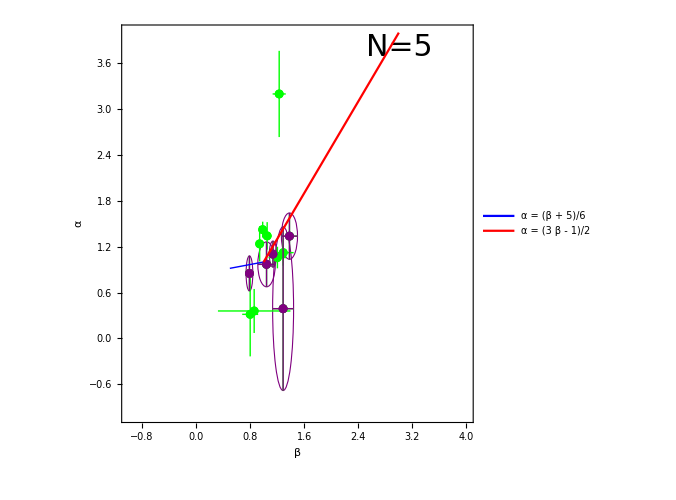

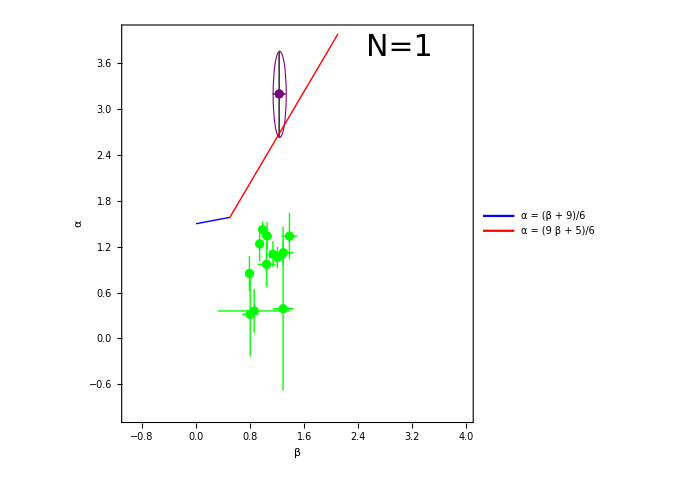

-Graphics-

```mathematica
(*Plots*)
"Total Number of GRBs considered: "<>ToString[Length[total]]
splplot=ListPlot[{}];
totalplot=ListPlot[plotTotal,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
(*bplplot=ListPlot[plotTotalBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Green];
splplot=ListPlot[plotTotalSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
*)
all={};

satbplplot=ListPlot[plotGreaterBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotGreaterSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[GreaterBPL]+Length[GreaterSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+(5-k)/2/(4-k)},{x,0.5,1.0},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Directive[Blue, Thick]},PlotLegends->Placed[{"α = (β + 5)/6"},{0.7,0.8}]]];
reg2=With[{t=.0004,d=.5,background=White},Plot[{(3*x-1)/2},{x,1.0,4.0},PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->{Red},PlotLegends->Placed[{"α = (3  β - 1)/2"},{0.7,0.65}]]];
Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"Greater.pdf",Show[txt,plotGreaterTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
AppendTo[all,reg2];



satbplplot=ListPlot[plotSlowBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotSlowBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
reg1=With[{t=.0004,d=.5,background=White},Plot[{(3-k)*x/2/(4-k)+9/4/(4-k)}, {x, 0, 0.5}, PlotStyle->{Directive[Blue, Thick]},PlotLegends->Placed[{"α = (β + 9)/6"},{0.65,0.8}]]];
reg2=With[{t=.0004,d=.5,background=White},Plot[{3*x/2+k/2/(4-k)}, {x, 0.5, 2.1}, PlotStyle->{Directive[Red, Thick]},PlotLegends->Placed[{"α = (9  β + 5)/6"},{0.65,0.65}]]];
Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"SlowBetween.pdf",Show[txt,plotSlowBetweenTotErr,totalplot,satbplplot,satsplplot,reg1,reg2,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,reg1];
AppendTo[all,reg2];





satbplplot=ListPlot[plotFastBetweenBPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
satsplplot=ListPlot[plotFastBetweenSPL,PlotRange->{{-1.0,4.0},{-1.0,4.0}},PlotStyle->Purple];
txt = Graphics[{Text[Style["N="<>ToString[Length[FastBetween]+Length[FastBetweenSPL]],FontSize->30],{3.0,3.8},{0,1}]}];
basereg=ListPlot[{{0.5,0.25}},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}, PlotLegends->Placed[{"α = β/2, β = 1/2"},{0.7,0.8}]];
Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,basereg,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->24,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]
Export["plotk"<>ToString[k]<>"FastBetween.pdf",Show[txt,plotFastBetweenTotErr,totalplot,satbplplot,satsplplot,basereg,PlotRange->{{-1.0,4.0},{-1.0,4.0}},AxesOrigin->{0,0},BaseStyle->{FontSize->18,Bold},Frame->True,FrameLabel->{{"α",""},{"β",""}},RotateLabel->False,AspectRatio->1,ImageSize->500]];
AppendTo[all,satbplplot];
AppendTo[all,satsplplot];
AppendTo[all,basereg];
```

```mathematica
summary={{"k","Cooling","v Range","CR: 1 < p < 2","CR: p > 2","GRBs Satisfying Relation","Proportion Satisfying Relation"},
(*{"ISM","Slow","v < v_m",   "[3β/2]",     ToString[Length[ismSlowLesser]+Length[ismSlowLesserSPL]],          ToString[DecimalForm[100.*(Length[ismSlowLesser]+Length[ismSlowLesserSPL])/Length[total],3]]<>"%"},*)
{ToString[k],"Slow","v_m < v < v_c","α=("<>ToString[2*(3-k)]<>"β+9)/"<>ToString[4*(4-k)],If[k==0,"α=3β/2","α=("<>ToString[3*(4-k)]<>"β+"<>ToString[k]<>")/"<>ToString[2*(4-k)]],ToString[Length[SlowBetween]+Length[SlowBetweenSPL]],ToString[DecimalForm[100.*(Length[SlowBetween]+Length[SlowBetweenSPL])/Length[total],3]]<>"%"},
{ToString[k],"","v > v_c,v_m","α=("<>ToString[3-k]<>"β+"<>ToString[5-k]<>")/"<>ToString[2*(4-k)],"(3β-1)/2",ToString[Length[GreaterBPL]+Length[GreaterSPL]],     ToString[DecimalForm[100.*(Length[GreaterBPL]+Length[GreaterSPL])/Length[total],3]]<>"%"},
(*{"ISM","Fast","v < v_c",   "[β/2]",        ToString[Length[ismFastLesser]+Length[ismFastLesserSPL]],          ToString[DecimalForm[100.*(Length[ismFastLesser]+Length[ismFastLesserSPL])/Length[total],3]]<>"%"},*)
{ToString[k],"Fast","v_c < v < v_m","β/2","β/2",ToString[Length[FastBetween]+Length[FastBetweenSPL]],ToString[DecimalForm[100.*(Length[FastBetween]+Length[FastBetweenSPL])/Length[total],3]]<>"%"}
};
"Total Number of GRBs: " <> ToString[Length[total]]
TableForm[Rest[summary],TableHeadings->{None,summary[[1,All]]}]
```

Total Number of GRBs: 13

k | Cooling | v Range | CR: 1 < p < 2 | CR: p > 2 | GRBs Satisfying Relation | Proportion Satisfying Relation
2.5 | Slow | v_m < v < v_c | α=(1.β+9)/6. | α=(4.5β+2.5)/3. | 1 | 7.69%
2.5 |  | v > v_c,v_m | α=(0.5β+2.5)/3. | (3β-1)/2 | 5 | 38.5%
2.5 | Fast | v_c < v < v_m | β/2 | β/2 | 1 | 7.69%

```mathematica
totalwithoutinj = DeleteDuplicates[Join[nototalsamplek0, noactualtotalk1, noactualtotalk15, noactualtotalk2, noactualtotalk25]]
```

{180720B,080916C,221009A,171010A,090926A,090323A,090902B,100414A,090510A}

```mathematica
Length[totalwithoutinj]
```

9

```mathematica
TOTAL = DeleteDuplicates[Join[totalwithoutinj, totalwithinj]]
```

{180720B,080916C,221009A,171010A,090926A,090323A,090902B,100414A,090510A,090328A,160509A,110731A}

```mathematica
Length[TOTAL]
```

12